```mathematica
ImportCsv[name_] := Import["~/workspace/PBLL/LieDetector/Analysis/" <> name <> ".csv","Dataset","HeaderLines"->1]
```

```mathematica
XY[name_] := Values[ImportCsv[name][All,{"Combine Gaze X","Combine Gaze Y"}]]
```

```mathematica
LP[name_] := ListPlot[Normal[XY[name]], PlotRange->{{-0.05, 0.05},{-0.15, 0.1}}]
```

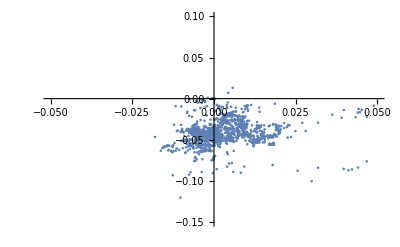
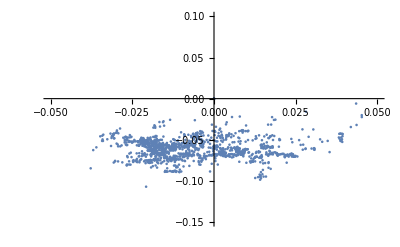
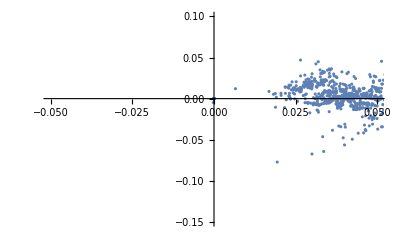

```mathematica
{LP["truth"], LP["truth2"], LP["truth3"]}
```

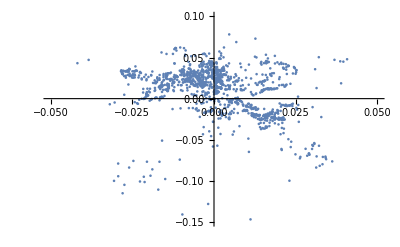
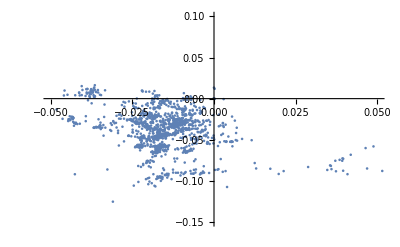
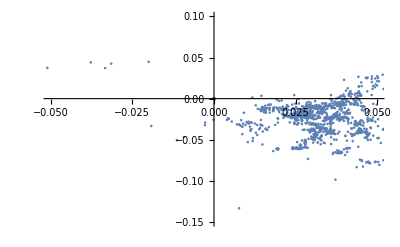

```mathematica
{LP["lies"], LP["lies2"], LP["lies3"]}
```

```mathematica
CenterPoint[name_] := 
Block[{xy},
xy = XY[name];
{Mean[xy[All, 1]], Mean[xy[All, 2]]}
]
```

```mathematica
ListPlotWithCenter[name_]:= 
Block[{xyValues, center},
xyValues = Normal[XY[name]];
center = {CenterPoint[name]};
ListPlot[{xyValues, center}, PlotRange->{{-0.1, 0.1},{-0.15, 0.15}},PlotStyle->{PointSize[0.01],PointSize[0.04]}]
]
```

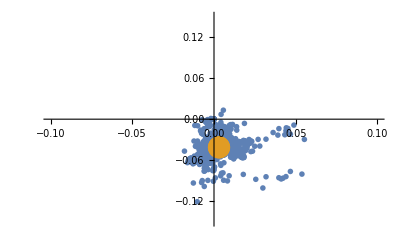
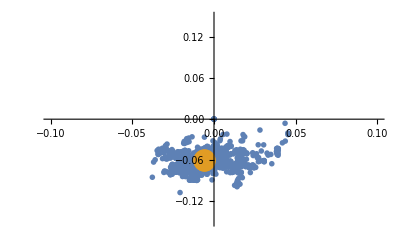
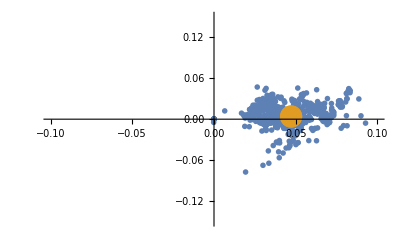

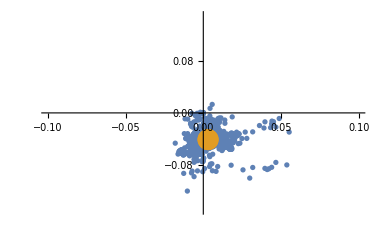
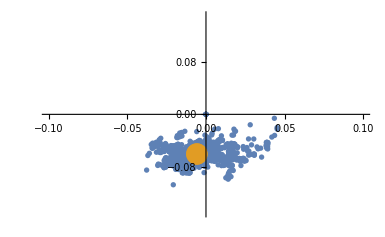
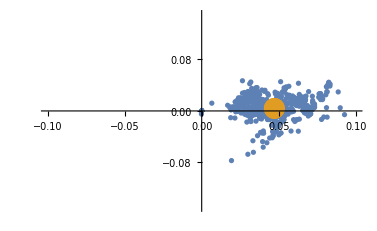

```mathematica
{ListPlotWithCenter["truth"],ListPlotWithCenter["truth2"],ListPlotWithCenter["truth3"]}
```

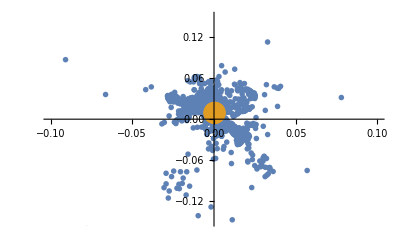
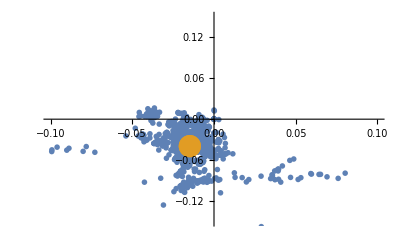
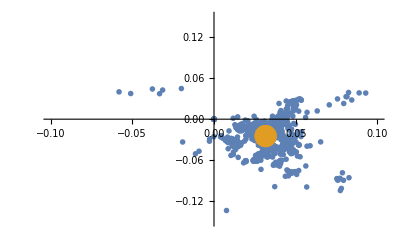

```mathematica
{ListPlotWithCenter["lies"],ListPlotWithCenter["lies2"],ListPlotWithCenter["lies3"]}
```

```mathematica
MeanFromCenter[name_]:= 
Block[{center,values},
center = CenterPoint[name];
values = Normal[XY[name]];
allDistances = (ArcLength[Line[{#, center}]])& /@ values;
Mean[allDistances]
]
```

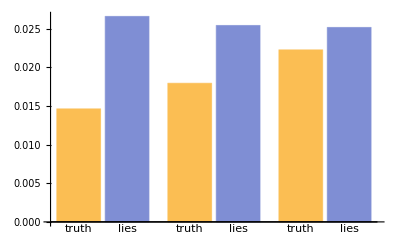

```mathematica
BarChart[{{MeanFromCenter["truth"], MeanFromCenter["lies"]}, {MeanFromCenter["truth2"], MeanFromCenter["lies2"]}, {MeanFromCenter["truth3"], MeanFromCenter["lies3"]}}, ChartLabels->{"truth","lies"}]
```

```mathematica
IndividualMeansFromCenter[name_] :=
Block[{columns, dataset, allValues, center, grouped, groupedColumns, groupedValues, allDistances, allMeans},
columns = {"Combine Gaze X","Combine Gaze Y"};
dataset=ImportCsv[name];
allValues=Values[dataset[All,columns]];
center={Mean[allValues[All,1]],Mean[allValues[All,2]]};

grouped=dataset[GroupBy["Index"]];
groupedColumns = Table[grouped[[x]][All, columns], {x, 1, Length[grouped], 1}];
groupedValues = (Normal[Values[#]])& /@ groupedColumns;
allDistances=((ArcLength[Line[{#,center}]])& /@ #)&/@groupedValues;
allMeans = (Mean[#])& /@ allDistances;
Drop[allMeans, 1]
]
```

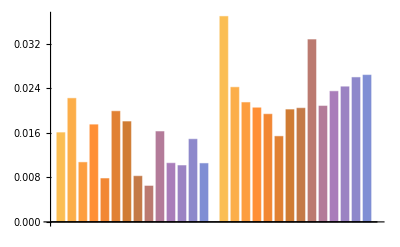

```mathematica
BarChart[{IndividualMeansFromCenter["truth"], IndividualMeansFromCenter["lies"]}]
```

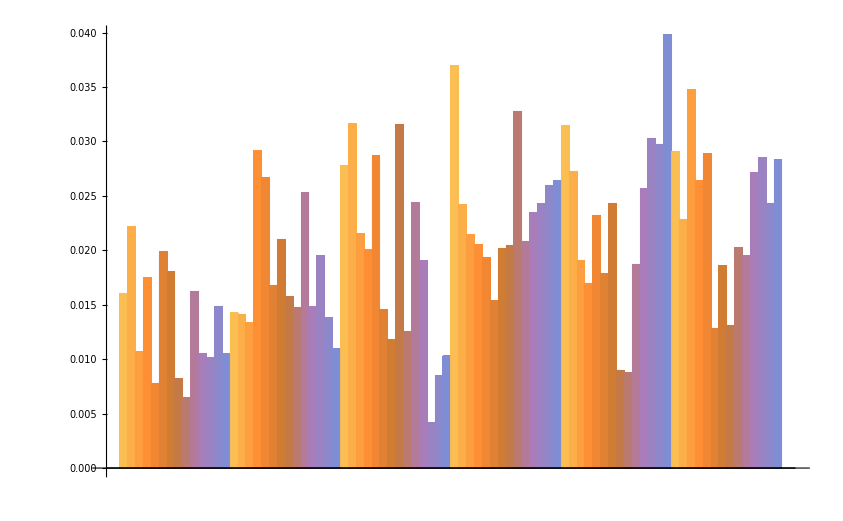

```mathematica
BarChart[{IndividualMeansFromCenter["truth"], IndividualMeansFromCenter["truth2"], IndividualMeansFromCenter["truth3"], IndividualMeansFromCenter["lies"], IndividualMeansFromCenter["lies2"], IndividualMeansFromCenter["lies3"]}]
```

```mathematica
colors = (If[# == "FALSE",Red,Blue])& /@Normal[Values[((#[[1]])&/@ImportCsv["mixed"][GroupBy["Index"]])[All, "Truth"]]]
```

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1]}

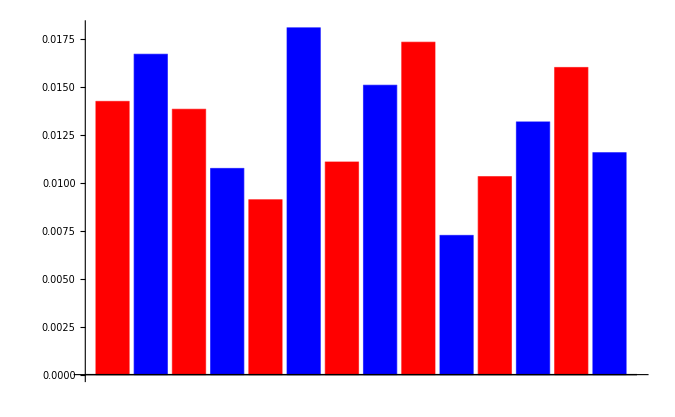

```mathematica
BarChart[IndividualMeansFromCenter["mixed"], ChartStyle-> colors]
```

```mathematica
TimeToAnswer[name_] := 
Block[{dataset, grouped, times},
dataset = ImportCsv[name][Select[#Truth =="TRUE"&]];
grouped = dataset[GroupBy["Index"]];
times = Table[grouped[[x]][All, "Total Time"], {x, 1, Length[grouped], 1}];
(Last[#] - First[#])& /@ times
]
```

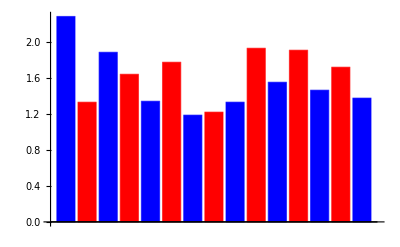

```mathematica
BarChart[TimeToAnswer["mixed"], ChartStyle-> colors]
```

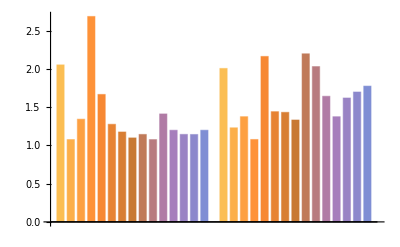

```mathematica
BarChart[{TimeToAnswer["truth3"], TimeToAnswer["lies3"]}]
```

```mathematica
Mean[TimeToAnswer["mixed"]]
```

1.55371